# Quantum phys

### outline

- On hilbert space -> space mechanics
- Born interpretation

- correspondence rules (with dimensional analysis)
- Hamiltonian
- t.d. Schrodinger equation
- stationary states (t.i Schrod)
- e.g. harmonic oscillator states
- GPE
- BdG

## The Schro^(..)dinger Equation

```mathematica
ClearAll["Global`*"]
```

```mathematica
<< Notation`
Symbolize[Ĥ]
Symbolize[K̂]
Symbolize[V̂]
Symbolize[P̂]
Symbolize[Schrod]
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

The time-dependent Schrodinger equation describes the evolution of the quantum wavefunction ψ, for a system with total energy given by the Hamiltonian Ĥ.

```mathematica
Schrod[ψ_] :=  
	ⅈ ℏ D[ψ, t] == Ĥ[ψ]
Schrod[ψ[t]]
```

ⅈ ℏ ψ'[t]==1/2 m r^2 ω^2 ψ[t]

We’ll assume the particular form of the Hamiltonian is time-independent.

```mathematica
Ĥ[c_ ψ_] := c Ĥ[ ψ ]   /;   D[c, r]==0
```

By substituting the wavefunction for an eigenfunction of the Hamiltonian...

```mathematica
Schrod[ψ[r, t]] /. Ĥ[ψ[r, t]] ->  Energy ψ[r, t]
```

ⅈ ℏ ψ^(0,1)[r,t]==Energy ψ[r,t]

we can realise the temporal form of the energy eigenfunctions in terms of a time-independent wavefunction ϕ...

```mathematica
DSolve[%, ψ[r, t], {r, t}][[1]][[1]]  /. C[1] -> ϕ
{%, Derivative[0,1][ψ][r,t]-> D[ψ[r, t] /. %, t]} ;
```

ψ[r,t]→ⅇ^(-(ⅈ Energy t)/ℏ) ϕ[r]

which when substituted back into the Schrodinger equation...

```mathematica
Schrod[ ψ[r, t] ] /. %
```

ⅇ^(-(ⅈ Energy t)/ℏ) Energy ϕ[r]==ⅇ^(-(ⅈ Energy t)/ℏ) Ĥ[ϕ[r]]

presents an equation for the time-independent eigenfunctions

```mathematica
SchrodTI = Simplify[%, Energy >0]
```

Ĥ[ϕ[r]]==Energy ϕ[r]

## The Correspondence rules

```mathematica
P̂[ψ_] := -ⅈ ℏ D[ψ, r]
```

```mathematica
K̂[ψ_] := (P̂[ P̂[ψ]])/(2m)
```

```mathematica
(*    V̂[ψ_] := 1/2 m ω^2 r^2           just a scalar potential quantity! *)
```

```mathematica
Ĥ[ψ_] := K̂[ψ] + V̂[ψ]
```

```mathematica
Ĥ[ψ[r]]
```

V̂[ψ[r]]-(ℏ^2 ψ''[r])/(2 m)

## The Quantum Harmonic Oscillator

```mathematica
assumps = {m > 0, ω >0, ℏ > 0};
naturalunits = {m -> 1, ω -> 1, ℏ -> 1};
```

A 1D harmonic trap, parametrized by the natural frequency ω, has a potential

```mathematica
V̂[ψ_] := 1/2 m ω^2 r^2 ψ
```

The time-independent Schrodinger equation then becomes

```mathematica
SchrodTI
```

1/2 m r^2 ω^2 ϕ[r]-(ℏ^2 ϕ''[r])/(2 m)==Energy ϕ[r]

which we can solve for the time-independent energy eigenfunctions ϕ[r] and their eigenvalues Energy

```mathematica
DSolve[SchrodTI, ϕ[r], r]  // Flatten
```

{ϕ[r]→C[2] ParabolicCylinderD[(-2 Energy-ω ℏ)/(2 ω ℏ),(ⅈ √2 √m r √ω)/(√ℏ)]+C[1] ParabolicCylinderD[(2 Energy-ω ℏ)/(2 ω ℏ),(√2 √m r √ω)/(√ℏ)]}

With two arbitrary constants (and one normalisation condition), we’ll arbitrarily set C[2] to 0, which presents a real basis.

```mathematica
ϕ[r] =  ϕ[r] /. FunctionExpand[Simplify[% , {Energy > 0  , C[2] == 0}] ]
```

2^(1/2 (1/2-Energy/(ω ℏ))) ⅇ^(-(m r^2 ω)/(2 ℏ)) C[1] HermiteH[-1/2+Energy/(ω ℏ),(√m r √ω)/(√ℏ)]

Enforcing the Hermite polynomials have integer order...

```mathematica
n ==Extract[ ϕ[r],  Position[ϕ[r], _HermiteH] // Flatten ][[1]]
```

n==-1/2+Energy/(ω ℏ)

lets us solve for the energy eigenvalue spectrum, parameterized by quantum number n...

```mathematica
Solve[%, Energy] // Flatten
```

{Energy→1/2 (1+2 n) ω ℏ}

which gives our energy eigenfunctions parameterized by n as

```mathematica
ϕ[r, n_] = ϕ[r] /. % //FullSimplify
```

2^(-n/2) ⅇ^(-(m r^2 ω)/(2 ℏ)) C[1] HermiteH[n,(√m r √ω)/(√ℏ)]

Our arbitrary complex constant is resolved with the normalisation condition ∫|ψ|^2 dr = 1; Mathematica will arbitrarily choose real values, and we’ll arbitrarily choose a positive one

```mathematica
numModes = 2;
Table[ 
{
      Solve[
         Integrate[
          Abs[ϕ[r,n1]]^2, {r, -∞, ∞},  
          Assumptions ->  assumps] == 1,
         C[1]][[2]] [[1]],
    n -> n1
},
    {n1, 0,numModes-1}]
```

{{C[1]→(m ω ℏ)^(1/4)/(π^(1/4) √ℏ),n→0},{C[1]→(√m √ω (ℏ/(m ω))^(1/4))/(π^(1/4) √ℏ),n→1}}

We now know the energy eigenfunctions to an arbitrarily phase

```mathematica
eigfuncs[r_] = ϕ[r, n] /. %
```

{(ⅇ^(-(m r^2 ω)/(2 ℏ)) (m ω ℏ)^(1/4))/(π^(1/4) √ℏ),(√2 ⅇ^(-(m r^2 ω)/(2 ℏ)) m r ω (ℏ/(m ω))^(1/4))/(π^(1/4) ℏ)}

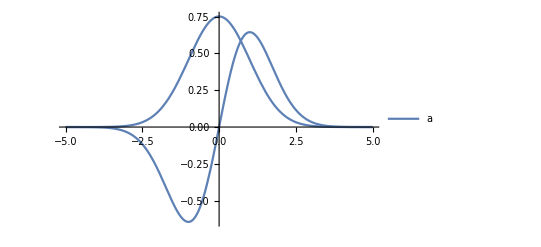

```mathematica
Plot[ 
eigfuncs[r]/. naturalunits,  {r, -5, 5}, 
PlotRange -> All, PlotLegends-> {"a", "b"}]
```

```mathematica
eigfuncs[r] /. naturalunits
```

{(ⅇ^(-r^2/2))/π^(1/4),(√2 ⅇ^(-r^2/2) r)/π^(1/4)}

```mathematica
Manipulate[
    Plot[
      eigfuncs[r]    /.    { ℏ -> 1, m -> m1, ω -> ω1},
       {r, 0, 5}, PlotRange->All],
   {m1, 0.01, 100},
   {ω1, 0.1, 10}
]
```

```mathematica
Manipulate[
   eigfuncs[r] /. m -> m1,
   {m1, 0.01, 100},
   {ℏ, 1, 10},
   {ω, 0.1, 10}
]
```

-Graphics-

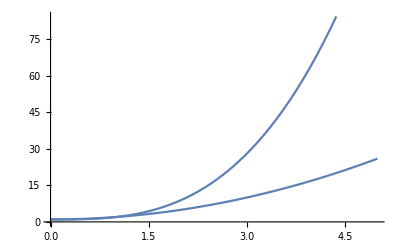

```mathematica
Plot[ {a x^2 + b,  a x^3 + b} /. {a -> 1, b -> 1}, {x, 0, 5}]
```

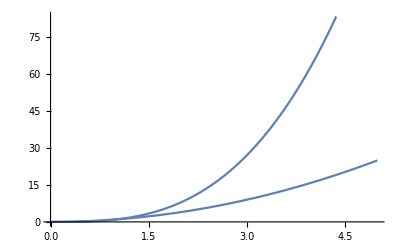

```mathematica
Plot[ {x^2, x^3}/. {a -> 1}, {x, 0, 5}]    (* this is the dumbest shit in the world *)
```

## Scratch

```mathematica
(* doesn't seem to scale the Jacobian; what gives *)
(* http://functions.wolfram.com/Polynomials/HermiteH/21/01/02/02/0001/ *)
(* arg[HermiteH] *= c *)
```

```mathematica
Integrate[ Exp[- r^2]  HermiteH[n, c r], r,  Assumptions -> {n  ∈ Integers, n ≥ 0}  ]
```

```mathematica
Integrate[ⅇ^(-r^2) HermiteH[n, r],r,Assumptions->{n∈Integers,n≥0}]
```

2^n √π ((r HypergeometricPFQ[{1/2+n/2},{3/2},-r^2])/Gamma[(1-n)/2]+(-1+HypergeometricPFQ[{n/2},{1/2},-r^2])/(n Gamma[-n/2]))